```mathematica
Needs["BenderWu`"]
```

BenderWu::shdw: Symbol BenderWu appears in multiple contexts {BenderWu`,Global`}; definitions in context BenderWu` may shadow or be shadowed by other definitions.

```mathematica
?BenderWu
```

```mathematica
BW=BenderWu[x^2/2+x^4,x,0,10];
```

```mathematica
BW
```

{{0,1/2,3/4,-21/8,333/16,-30885/128,916731/256,-65518401/1024,2723294673/2048,-1030495099053/32768,54626982511455/65536,-6417007431590595/262144},{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-3/4,0,-1/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,21/8,0,31/32,0,13/48,0,1/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-333/16,0,-243/32,0,-271/128,0,-47/128,0,-17/384,0,-1/384,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,30885/128,0,2777/32,0,18461/768,0,9195/2048,0,979/1536,0,599/9216,0,7/1536,0,1/6144,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-916731/256,0,-651363/512,0,-89673/256,0,-69107/1024,0,-250183/24576,0,-29177/24576,0,-1325/12288,0,-269/36864,0,-25/73728,0,-1/122880,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,65518401/1024,0,23046319/1024,0,75770813/12288,0,2476011/2048,0,9259481/49152,0,13796435/589824,0,77173/32768,0,112483/589824,0,4055/331776,0,349/589824,0,29/1474560,0,1/2949120,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-2723294673/2048,0,-1900738887/4096,0,-1037387179/8192,0,-411558719/16384,0,-392840431/98304,0,-101245699/196608,0,-43151765/786432,0,-11441483/2359296,0,-838357/2359296,0,-150911/7077888,0,-108553/106168320,0,-1319/35389440,0,-11/11796480,0,-1/82575360,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1030495099053/32768,0,178679039237/16384,0,291628341269/98304,0,19448990361/32768,0,75358651093/786432,0,3733838213/294912,0,2200420397/1572864,0,3280019929/25165824,0,291395659/28311552,0,38950649/56623104,0,16409753/424673280,0,9150343/5096079360,0,28487/424673280,0,541/283115520,0,37/990904320,0,1/2642411520,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-54626982511455/65536,0,-37696919264379/131072,0,-10228319926141/131072,0,-2060259959333/131072,0,-4036187405567/1572864,0,-1086164645615/3145728,0,-15391050197/393216,0,-71320205783/18874368,0,-31524603955/100663296,0,-750036419/33554432,0,-311114717/226492416,0,-245686033/3397386240,0,-21934507/6794772480,0,-489047/4076863488,0,-36661/10192158720,0,-653/7927234560,0,-41/31708938240,0,-1/95126814720,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,6417007431590595/262144,0,2205170498765479/262144,0,7165277933588117/3145728,0,120939235709331/262144,0,478056886880743/6291456,0,195680278973305/18874368,0,30147016064305/25165824,0,497736819293/4194304,0,6145563206639/603979776,0,5503872304091/7247757312,0,2689270862993/54358179840,0,917469605837/326149079040,0,35015249/251658240,0,969209047/163074539520,0,74153917/342456532992,0,7527391/1141521776640,0,18541/114152177664,0,2327/761014517760,0,1/25367150592,0,1/3805072588800,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{x,0,20,1}}

```mathematica
BW[[1]]
```

{0,1/2,3/4,-21/8,333/16,-30885/128,916731/256,-65518401/1024,2723294673/2048,-1030495099053/32768,54626982511455/65536,-6417007431590595/262144}

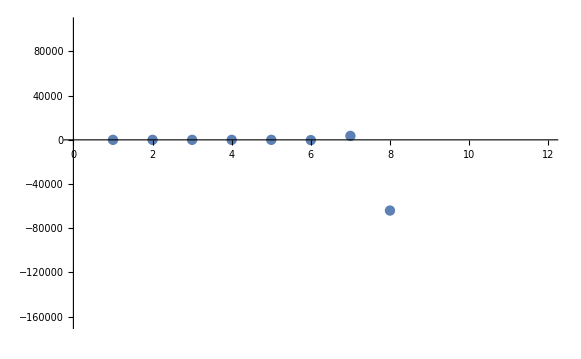

```mathematica
ListPlot[BW[[1]]]
```

```mathematica
Plot
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
BWProcess[BW,OutputStyle->"Series",Order->10]
```

1/2+(3 g^2)/4-(21 g^4)/8+(333 g^6)/16-(30885 g^8)/128+(916731 g^10)/256-(65518401 g^12)/1024+(2723294673 g^14)/2048-(1030495099053 g^16)/32768+(54626982511455 g^18)/65536-(6417007431590595 g^20)/262144